```mathematica
(*finite difference method for solving bundary value problems *)
```

```mathematica
(*Problem:-Solve the differnetial equation of simple harmonic oscillaior*)
deq=x''[t]+w^2 x[t]==0;
(*Define the rules of finite difference method*)
FDRules={x''[t]->(x[i+1]-2 x[i]+x[i-1])/h^2,x'[t]->(x[i+1]-x[i-1])/(2 h),x[t]->x[i],t->i}
```

{x''[t]→(55696 (x[-1+i]-2 x[i]+x[1+i]))/(25 π^2),x'[t]→(118 (-x[-1+i]+x[1+i]))/(5 π),x[t]→x[i],t→i}

```mathematica
(*Apply the finite difference rules on the differential equation*)
fdeq=deq/.FDRules
```

4 x[i]+(55696 (x[-1+i]-2 x[i]+x[1+i]))/(25 π^2)==0

```mathematica
(*Define the Given information*)
ω=2;T=(2*π)/ω;tmin=0;tmax=(5T)/4;n=60;h=(tmax-tmin)/(n-1);
(*Generate list of algebraic equations*)
aeqs=Table[fdeq,{i,2,n-1}]
```

{4 x[2]+(55696 (x[1]-2 x[2]+x[3]))/(25 π^2)==0,4 x[3]+(55696 (x[2]-2 x[3]+x[4]))/(25 π^2)==0,4 x[4]+(55696 (x[3]-2 x[4]+x[5]))/(25 π^2)==0,4 x[5]+(55696 (x[4]-2 x[5]+x[6]))/(25 π^2)==0,4 x[6]+(55696 (x[5]-2 x[6]+x[7]))/(25 π^2)==0,4 x[7]+(55696 (x[6]-2 x[7]+x[8]))/(25 π^2)==0,4 x[8]+(55696 (x[7]-2 x[8]+x[9]))/(25 π^2)==0,4 x[9]+(55696 (x[8]-2 x[9]+x[10]))/(25 π^2)==0,4 x[10]+(55696 (x[9]-2 x[10]+x[11]))/(25 π^2)==0,4 x[11]+(55696 (x[10]-2 x[11]+x[12]))/(25 π^2)==0,4 x[12]+(55696 (x[11]-2 x[12]+x[13]))/(25 π^2)==0,4 x[13]+(55696 (x[12]-2 x[13]+x[14]))/(25 π^2)==0,4 x[14]+(55696 (x[13]-2 x[14]+x[15]))/(25 π^2)==0,4 x[15]+(55696 (x[14]-2 x[15]+x[16]))/(25 π^2)==0,4 x[16]+(55696 (x[15]-2 x[16]+x[17]))/(25 π^2)==0,4 x[17]+(55696 (x[16]-2 x[17]+x[18]))/(25 π^2)==0,4 x[18]+(55696 (x[17]-2 x[18]+x[19]))/(25 π^2)==0,4 x[19]+(55696 (x[18]-2 x[19]+x[20]))/(25 π^2)==0,4 x[20]+(55696 (x[19]-2 x[20]+x[21]))/(25 π^2)==0,4 x[21]+(55696 (x[20]-2 x[21]+x[22]))/(25 π^2)==0,4 x[22]+(55696 (x[21]-2 x[22]+x[23]))/(25 π^2)==0,4 x[23]+(55696 (x[22]-2 x[23]+x[24]))/(25 π^2)==0,4 x[24]+(55696 (x[23]-2 x[24]+x[25]))/(25 π^2)==0,4 x[25]+(55696 (x[24]-2 x[25]+x[26]))/(25 π^2)==0,4 x[26]+(55696 (x[25]-2 x[26]+x[27]))/(25 π^2)==0,4 x[27]+(55696 (x[26]-2 x[27]+x[28]))/(25 π^2)==0,4 x[28]+(55696 (x[27]-2 x[28]+x[29]))/(25 π^2)==0,4 x[29]+(55696 (x[28]-2 x[29]+x[30]))/(25 π^2)==0,4 x[30]+(55696 (x[29]-2 x[30]+x[31]))/(25 π^2)==0,4 x[31]+(55696 (x[30]-2 x[31]+x[32]))/(25 π^2)==0,4 x[32]+(55696 (x[31]-2 x[32]+x[33]))/(25 π^2)==0,4 x[33]+(55696 (x[32]-2 x[33]+x[34]))/(25 π^2)==0,4 x[34]+(55696 (x[33]-2 x[34]+x[35]))/(25 π^2)==0,4 x[35]+(55696 (x[34]-2 x[35]+x[36]))/(25 π^2)==0,4 x[36]+(55696 (x[35]-2 x[36]+x[37]))/(25 π^2)==0,4 x[37]+(55696 (x[36]-2 x[37]+x[38]))/(25 π^2)==0,4 x[38]+(55696 (x[37]-2 x[38]+x[39]))/(25 π^2)==0,4 x[39]+(55696 (x[38]-2 x[39]+x[40]))/(25 π^2)==0,4 x[40]+(55696 (x[39]-2 x[40]+x[41]))/(25 π^2)==0,4 x[41]+(55696 (x[40]-2 x[41]+x[42]))/(25 π^2)==0,4 x[42]+(55696 (x[41]-2 x[42]+x[43]))/(25 π^2)==0,4 x[43]+(55696 (x[42]-2 x[43]+x[44]))/(25 π^2)==0,4 x[44]+(55696 (x[43]-2 x[44]+x[45]))/(25 π^2)==0,4 x[45]+(55696 (x[44]-2 x[45]+x[46]))/(25 π^2)==0,4 x[46]+(55696 (x[45]-2 x[46]+x[47]))/(25 π^2)==0,4 x[47]+(55696 (x[46]-2 x[47]+x[48]))/(25 π^2)==0,4 x[48]+(55696 (x[47]-2 x[48]+x[49]))/(25 π^2)==0,4 x[49]+(55696 (x[48]-2 x[49]+x[50]))/(25 π^2)==0,4 x[50]+(55696 (x[49]-2 x[50]+x[51]))/(25 π^2)==0,4 x[51]+(55696 (x[50]-2 x[51]+x[52]))/(25 π^2)==0,4 x[52]+(55696 (x[51]-2 x[52]+x[53]))/(25 π^2)==0,4 x[53]+(55696 (x[52]-2 x[53]+x[54]))/(25 π^2)==0,4 x[54]+(55696 (x[53]-2 x[54]+x[55]))/(25 π^2)==0,4 x[55]+(55696 (x[54]-2 x[55]+x[56]))/(25 π^2)==0,4 x[56]+(55696 (x[55]-2 x[56]+x[57]))/(25 π^2)==0,4 x[57]+(55696 (x[56]-2 x[57]+x[58]))/(25 π^2)==0,4 x[58]+(55696 (x[57]-2 x[58]+x[59]))/(25 π^2)==0,4 x[59]+(55696 (x[58]-2 x[59]+x[60]))/(25 π^2)==0}

```mathematica
(*include the boundary conditions among the aeqs*)
```

```mathematica
a=2;
aeqs=Join[{x[1]==a,x[20]==0},aeqs]
```

{x[1]==2,x[20]==0,4 x[2]+(55696 (x[1]-2 x[2]+x[3]))/(25 π^2)==0,4 x[3]+(55696 (x[2]-2 x[3]+x[4]))/(25 π^2)==0,4 x[4]+(55696 (x[3]-2 x[4]+x[5]))/(25 π^2)==0,4 x[5]+(55696 (x[4]-2 x[5]+x[6]))/(25 π^2)==0,4 x[6]+(55696 (x[5]-2 x[6]+x[7]))/(25 π^2)==0,4 x[7]+(55696 (x[6]-2 x[7]+x[8]))/(25 π^2)==0,4 x[8]+(55696 (x[7]-2 x[8]+x[9]))/(25 π^2)==0,4 x[9]+(55696 (x[8]-2 x[9]+x[10]))/(25 π^2)==0,4 x[10]+(55696 (x[9]-2 x[10]+x[11]))/(25 π^2)==0,4 x[11]+(55696 (x[10]-2 x[11]+x[12]))/(25 π^2)==0,4 x[12]+(55696 (x[11]-2 x[12]+x[13]))/(25 π^2)==0,4 x[13]+(55696 (x[12]-2 x[13]+x[14]))/(25 π^2)==0,4 x[14]+(55696 (x[13]-2 x[14]+x[15]))/(25 π^2)==0,4 x[15]+(55696 (x[14]-2 x[15]+x[16]))/(25 π^2)==0,4 x[16]+(55696 (x[15]-2 x[16]+x[17]))/(25 π^2)==0,4 x[17]+(55696 (x[16]-2 x[17]+x[18]))/(25 π^2)==0,4 x[18]+(55696 (x[17]-2 x[18]+x[19]))/(25 π^2)==0,4 x[19]+(55696 (x[18]-2 x[19]+x[20]))/(25 π^2)==0,4 x[20]+(55696 (x[19]-2 x[20]+x[21]))/(25 π^2)==0,4 x[21]+(55696 (x[20]-2 x[21]+x[22]))/(25 π^2)==0,4 x[22]+(55696 (x[21]-2 x[22]+x[23]))/(25 π^2)==0,4 x[23]+(55696 (x[22]-2 x[23]+x[24]))/(25 π^2)==0,4 x[24]+(55696 (x[23]-2 x[24]+x[25]))/(25 π^2)==0,4 x[25]+(55696 (x[24]-2 x[25]+x[26]))/(25 π^2)==0,4 x[26]+(55696 (x[25]-2 x[26]+x[27]))/(25 π^2)==0,4 x[27]+(55696 (x[26]-2 x[27]+x[28]))/(25 π^2)==0,4 x[28]+(55696 (x[27]-2 x[28]+x[29]))/(25 π^2)==0,4 x[29]+(55696 (x[28]-2 x[29]+x[30]))/(25 π^2)==0,4 x[30]+(55696 (x[29]-2 x[30]+x[31]))/(25 π^2)==0,4 x[31]+(55696 (x[30]-2 x[31]+x[32]))/(25 π^2)==0,4 x[32]+(55696 (x[31]-2 x[32]+x[33]))/(25 π^2)==0,4 x[33]+(55696 (x[32]-2 x[33]+x[34]))/(25 π^2)==0,4 x[34]+(55696 (x[33]-2 x[34]+x[35]))/(25 π^2)==0,4 x[35]+(55696 (x[34]-2 x[35]+x[36]))/(25 π^2)==0,4 x[36]+(55696 (x[35]-2 x[36]+x[37]))/(25 π^2)==0,4 x[37]+(55696 (x[36]-2 x[37]+x[38]))/(25 π^2)==0,4 x[38]+(55696 (x[37]-2 x[38]+x[39]))/(25 π^2)==0,4 x[39]+(55696 (x[38]-2 x[39]+x[40]))/(25 π^2)==0,4 x[40]+(55696 (x[39]-2 x[40]+x[41]))/(25 π^2)==0,4 x[41]+(55696 (x[40]-2 x[41]+x[42]))/(25 π^2)==0,4 x[42]+(55696 (x[41]-2 x[42]+x[43]))/(25 π^2)==0,4 x[43]+(55696 (x[42]-2 x[43]+x[44]))/(25 π^2)==0,4 x[44]+(55696 (x[43]-2 x[44]+x[45]))/(25 π^2)==0,4 x[45]+(55696 (x[44]-2 x[45]+x[46]))/(25 π^2)==0,4 x[46]+(55696 (x[45]-2 x[46]+x[47]))/(25 π^2)==0,4 x[47]+(55696 (x[46]-2 x[47]+x[48]))/(25 π^2)==0,4 x[48]+(55696 (x[47]-2 x[48]+x[49]))/(25 π^2)==0,4 x[49]+(55696 (x[48]-2 x[49]+x[50]))/(25 π^2)==0,4 x[50]+(55696 (x[49]-2 x[50]+x[51]))/(25 π^2)==0,4 x[51]+(55696 (x[50]-2 x[51]+x[52]))/(25 π^2)==0,4 x[52]+(55696 (x[51]-2 x[52]+x[53]))/(25 π^2)==0,4 x[53]+(55696 (x[52]-2 x[53]+x[54]))/(25 π^2)==0,4 x[54]+(55696 (x[53]-2 x[54]+x[55]))/(25 π^2)==0,4 x[55]+(55696 (x[54]-2 x[55]+x[56]))/(25 π^2)==0,4 x[56]+(55696 (x[55]-2 x[56]+x[57]))/(25 π^2)==0,4 x[57]+(55696 (x[56]-2 x[57]+x[58]))/(25 π^2)==0,4 x[58]+(55696 (x[57]-2 x[58]+x[59]))/(25 π^2)==0,4 x[59]+(55696 (x[58]-2 x[59]+x[60]))/(25 π^2)==0}

```mathematica
(*geberate the list of unknowns*)
```

```mathematica
unknowns=Table[x[i],{i,1,n}]
```

{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],x[13],x[14],x[15],x[16],x[17],x[18],x[19],x[20],x[21],x[22],x[23],x[24],x[25],x[26],x[27],x[28],x[29],x[30],x[31],x[32],x[33],x[34],x[35],x[36],x[37],x[38],x[39],x[40],x[41],x[42],x[43],x[44],x[45],x[46],x[47],x[48],x[49],x[50],x[51],x[52],x[53],x[54],x[55],x[56],x[57],x[58],x[59],x[60]}

```mathematica
(*use the Sove command to get values of unknowns *)
```

```mathematica
knowns=Solve[aeqs,unknowns]
```

```mathematica
{{x[60]->(5 (-3235091412729941114711322750074381721759185193494646270828716158238944145063668815103064839824435860988137717255554807714394249036662740117784349493493495960174592+1547960107534705018440404181440000590435260798021982245001172177841637845912574941153703640859688589761093618300426163918209687173711972567849628590950906121420800 π^2-221788309001130171774533635591266961930360908650808286324140943320458740490921215713993016627052480362926010378436526645850928318841955276706406854276576968704000 π^4+15084660248354934580806136981099170002428327145979363463808131934876483227018767450212842909708848727164098409738431839746926638968582459766277705894671155200000 π^6-595846246523643638282345255645255925117464803956381061842464274934075393195943844988298161472268514790308397397022228659926001970175262343540127710576640000000 π^8+15317859259923002962424162623744451732456828403399300299056586943099696147325930960548327353667031919947502773176301385106543526922547697093894471680000000000 π^10-275731395829645463574599455003171089365650707583342836245254711232403615672093517076878696591193285560233280312536086077933070690834316213092352000000000000 π^12+3656408555729231764991277091882449963117161935727321950250253562891222485904921315938212698979329847607435412688809570892277402510601979166720000000000000 π^14-37072598026894554624174362592383358025420301154779613196852698476346105607633925166245798526244958490029255413645263236314217373411311616000000000000000 π^16+295638291676813796166033618474760651602293808904301675081285294909047477545165465532225943138724735166102403509859469240503670879027200000000000000000 π^18-1895739445746384686294691709553139566333910930409863205624444015658007484156117043107904281012260018455431548750996924891398144000000000000000000000 π^20+9948836598915935203264109337863383645776161024883911310179003562954801889914026180081305402454134724357633919406097144217600000000000000000000000 π^22-43346937206805999401370963791322795737126814768957001303566471522976490088201492980340840353505997314782375115673409945600000000000000000000000 π^24+158648851454649275205004438997145781361713669725951944421434973283384110906644250654519074614930077680172162697134080000000000000000000000000 π^26-492520152154110134086063950325678677723064352100434134456186465641666150094815663458565668854715687993622921216000000000000000000000000000 π^28+1307433921649749628490797068297424462962559972527702101108892957810315438147276338169741335211490006794240000000000000000000000000000000 π^30-2987659453771201914103699132329389164796531759321353159933878295380183354780148849334108976809312256000000000000000000000000000000000 π^32+5909664384410397302930719890093383884436661469088940793650094578919748590362048149554087236771840000000000000000000000000000000000 π^34-10164482235540535901645503113748926277264561721154716084087427904826327693997646165131055872000000000000000000000000000000000000 π^36+15257534406261526305393219008663814061288841532303534916586323023267406732052323465466400000000000000000000000000000000000000 π^38-20044616427673826432418694965173065887232136737459188184359243326929034705893390950000000000000000000000000000000000000000 π^40+23096141631371803875656096336602845445221503108628297072647221262433370324335468750000000000000000000000000000000000000 π^42-23372998569263205457723061112098411141060124976086978965424768846969081509179687500000000000000000000000000000000000 π^44+20788550449101861743004211353653245353256546049597938358889720949725401000976562500000000000000000000000000000000 π^46-16250354557668245103548875707116178088833294091812649316026336125732421875000000000000000000000000000000000000 π^48+11155865520477084971047418348371744678825431712994725627584532928466796875000000000000000000000000000000000 π^50-6715402104140199368393676908509643843086903457932377307133674621582031250000000000000000000000000000000 π^52+3535979367012382787144941579996012376064033101204458543658256530761718750000000000000000000000000000 π^54-1622979343266521681109481731654227416962991435798518359661102294921875000000000000000000000000000 π^56+646324705630059063618724739890871335199985243729315698146820068359375000000000000000000000000 π^58-221944151712850902034300232253981574566376366419717669486999511718750000000000000000000000 π^60+65191101478187440031746219478951784151377069065347313880920410156250000000000000000000 π^62-16206657937144690967607561247612480315183347556740045547485351562500000000000000000 π^64+3362572228484114174745130523414005097038170788437128067016601562500000000000000 π^66-571310995412400530839178436348646528131212107837200164794921875000000000000 π^68+77396880304973405162623223407791783756692893803119659423828125000000000 π^70-8037438756437395841886184300051354512106627225875854492187500000000 π^72+600637810125312972958644408549844229128211736679077148437500000 π^74-28748086471574139932894098592441878281533718109130859375000 π^76+661744490042422139897126953655970282852649688720703125 π^78))/(522413403668714259831960338528714607508340040292051751413833543027275928596385168883712 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[1]->2,x[2]->-(27848 (-500334849432819479007465749300533530372947092417630124642724365343916032+48360192343795093519406371799313035738790909835204960936632184838553600 π^2-1389261486463518917535374082140564083274659863119935677582079426560000 π^4+18707736908353188526133484659677949268457248228597237830123520000000 π^6-143686335139087937345618109299211801931837127102882643968000000000 π^8+701245302528454683645305272134188333707974801581342720000000000 π^10-2324415958704797528269855939277578283344667099136000000000000 π^12+5465164538137468368030279880758591092459264000000000000000 π^14-9379586214316147001843204292031438022000000000000000000 π^16+11965747695503786015520651387837018750000000000000000 π^18-11458151580488160505142824272562500000000000000000 π^20+8253460523556082335671998242187500000000000000 π^22-4445630129752270720880493164062500000000000 π^24+1762397659004196268081665039062500000000 π^26-498808495663070678710937500000000000 π^28+95337131738662719726562500000000 π^30-11022575199604034423828125000 π^32+582076609134674072265625 π^34))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[59]->-(1132653737220515867151515254712195553977020096113645545122808910615832570179932883771002664043674577873970940219824022379177819883203882366719240432403102040064-515187709642578796224236087320016171731384224508265473459096267875630059212360547535407704127880326046285738393580781988039322459563194603266914876368355328000 π^2+70161210457464812003749474330693813964782916958043550994456427604076666172180313721920199580041156870530690277853171347660123902179453301238500957649633280000 π^4-4534982003139782447814889894974463700682607387405860090132920485756176354134033492511360214165257195021374694776490535255250754952708127773244100968448000000 π^6+170198436221366699582490695819382797027298093371103336656184299367774401636954788450536970596300354666083364146403348723406039188028307745487716352000000000 π^8-4155951473374366407501209176859390332467778780966326807174853618575358844912713880579041223983203144675979877174456949580440485774894041472696320000000000 π^10+71031063524804687386509545725746021485162257770836041586730180222678697691029923806385260572216398519663407647053654938702891260612989419520000000000000 π^12-893949172279726849093566190170946221889567545576245991980845211486359993375569826703799397086757864298577790116268758889846376380130918400000000000000 π^14+8597644196723666521155059312786406704760585258951630346751664188681482765344097722110652428013933624728488265337749870769749612298240000000000000000 π^16-64996780997018903530103715756107642274305517614052452764266651965417399456781155763699575348991772061329081671462751710562222080000000000000000000 π^18+394832260317761820615814849016382127432371566948334048858868690420010176964431156636952198717003307492153942213292953331302400000000000000000000 π^20-1961399873611131194632170307299674015254607003120226303328799616424275569601877510422662459434660511981102946410561536000000000000000000000000 π^22+8082111300519868736858716703628181314653337891699438678073102412549756593357348618249084933213419051631412061929472000000000000000000000000 π^24-27947334978975361906211315699821878847737823473483753820993948993782873087141182301073048435361924434019693363200000000000000000000000000 π^26+81879700143721693905484260842869006771392644744159121483587235741656118348617306026791881599103414566912000000000000000000000000000000 π^28-204868076830025274109967940502586685586047892067749930966894511683212572899210206811481758409781411840000000000000000000000000000000 π^30+440632870767441904165887009349068096646593179712771901280928104568577745772608853256225802741760000000000000000000000000000000000 π^32-819061726421052257773249252723143968621681561559472584634268237702883756104347531273718476800000000000000000000000000000000000 π^34+1321546814148426767071464089470471796541792118695139611126880813587510039561750051187680000000000000000000000000000000000000 π^36-1857241296123450584698681341405865991811339223131811786573398816732407735461308540000000000000000000000000000000000000000 π^38+2279324141325545234941798359776215239020220470720366366841578229505719497581959375000000000000000000000000000000000000 π^40-2447304979753630185419971496666041991501800499875844439531519953305065118359375000000000000000000000000000000000000 π^42+2301323403530887101299288527731608625383545957973924359033260455366426879882812500000000000000000000000000000000 π^44-1895874698394628595414035499163554110363884310711475753536405881335449218750000000000000000000000000000000000 π^46+1367666205635411859431294076362882160144463984045026459150988411903381347656250000000000000000000000000000 π^48-862827421865286221878460305820633027111771838231311508552932739257812500000000000000000000000000000000 π^50+474982303031514105735887674924837483351885043445375028252601623535156250000000000000000000000000000 π^52-227416596299681176738431329562787265800959993988975882530212402343750000000000000000000000000000 π^54+94276348792244761965186532817841505074780456267762929201126098632812500000000000000000000000 π^56-33636256532879267140602022776379816269686853047460317611694335937500000000000000000000000 π^58+10246939330937631419074476188522562128582649165764451026916503906250000000000000000000 π^60-2637703326233251738076973974572297265694942325353622436523437500000000000000000000 π^62+565802678628491357713963743323315469524459331296384334564208984375000000000000 π^64-99244398018325927089871352215766364679438993334770202636718750000000000000 π^66+13861711535701543194891438570692798748495988547801971435546875000000000 π^68-1482272915924033422629957357230523484759032726287841796875000000000 π^70+113928224408594907721137268197253433754667639732360839843750000 π^72-5602191209845217012563978187245083972811698913574218750000 π^74+132348898008484427979425390731194056570529937744140625 π^76)/(37518917241361265428896893028491425417145937969839970655977703463607866173253746688 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[3]->(387755552 (33936977083364977908355348631096867185116427954529797148513813921792-2924761024133724036916577015032766491104547080252496163330693529600 π^2+74830947633412754104533938638711797073828992914388951320494080000 π^4-895707024243665063972684317709372271782880792329658040320000000 π^6+6097785239377866814307002366384246380069346100707328000000000 π^8-26276006489706406841311414965746537116070149816320000000000 π^10+76512303533924557152423918330620275294429696000000000000 π^12-156999843095014891353929327226618531814400000000000000 π^14+233178673040586599276812693711695750000000000000000 π^16-254625590677514677892062761612500000000000000000 π^18+205726651473860968564040941406250000000000000 π^20-122638072544890226782910156250000000000000 π^22+53213038994449280868530273437500000000 π^24-16331955583806991577148437500000000 π^26+3358467140793800354003906250000 π^28-414967536926269531250000000 π^30+23283064365386962890625 π^32))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[4]->-(5399108306048 (-2293930215006842381895354521594326659689840847256859735945641984+175043152358860243519377634242600694909541503893307488468992000 π^2-3959967896656203440721341194083540569987472976615330283520000 π^4+41813384498591086726676587655206260891904087547707392000000 π^6-250247680854346731822013475864252734438763331584000000000 π^8+943550936861045922195899704314368612326563840000000000 π^10-2389128047098052694516315849100716788480000000000000 π^12+4228306604469303666886203512638749600000000000000 π^14-5358889354566770451636028582860000000000000000 π^16+4923372855784706939994142187500000000000000 π^18-3283326175011346812283203125000000000000 π^20+1572799182101949188232421875000000000 π^22-527127945739425659179687500000000 π^24+117293562078475952148437500000 π^26-15561282634735107421875000 π^28+931322574615478515625 π^30))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[5]->(375885920267061760 (30889968063328278268125464866341299101683794804701321494528-2070571449232001799069982323703812062738547961628930867200 π^2+41079816349492997485857700152483344034151384257396736000 π^4-379322800452904519814420426573183092201914944716800000 π^6+1976963867708858122696170809039629473446133760000000 π^8-6453748490862272213758359696272066129920000000000 π^10+14038646433811126799147869370025888000000000000 π^12-21124897165828428447028982239680000000000000 π^14+22450580222378263646373288375000000000000 π^16-16972270689289423521956250000000000000 π^18+9069360525852835205078125000000000 π^20-3346844099932861328125000000000 π^22+811232320976257324218750000 π^24-116190910339355468750000 π^26+7450580596923828125 π^28))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[6]->-(1046767110759713589248 (-10352857246160008995349911618519060313692739808144654336+604114946316073492439083825771813882855167415549952000 π^2-10412782757530712308631148964754045668287861227520000 π^4+83240583903530868324049297222721240987205632000000 π^6-373638070523605233428115561363119618048000000000 π^8+1042870877940255133650984581773351680000000000 π^10-1920445196893493495184452930880000000000000 π^12+2413659217583750083720764600000000000000 π^14-2103085715846732914677187500000000000 π^16+1269710473619396928710937500000000 π^18-521077881404931640625000000000 π^20+138672191619873046875000000 π^22-21578311920166015625000 π^24+1490116119384765625 π^26))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[7]->(14575185250218252016689152 (690417081504083991358952943739215866120191332057088-34709275858435707695437163215846818894292870758400 π^2+514133018227690657295598600493278253156270080000 π^4-3516593604928049255794028812829361111040000000 π^6+13417052230810299965100386432171776000000000 π^8-31535731654251051078818384970240000000000 π^10+48273184351675001674415292000000000000 π^12-49527213394832151756900000000000000 π^14+34327350353978952539062500000000 π^16-15858892042758789062500000000 π^18+4677875263977050781250000 π^20-796737670898437500000 π^22+59604644775390625 π^24))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[8]->-(202944879424038941080379752448 (-45770473659475658499477577867050750190276313088+1958601974200726313507042287593440964404838400 π^2-24616155234496344790558201689805527777280000 π^4+142062905973285529042239385752407040000000 π^6-453454964963087008976473509376000000000 π^8+880773889925298276164770240000000000 π^10-1094812085569973880942000000000000 π^12+889241837741169056250000000000 π^14-469587972175195312500000000 π^16+155312854614257812500000 π^18-29213714599609375000 π^20+2384185791015625 π^22))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[9]->(2825804501100318215603207673085952 (3013233806462655866933911211682216868315136-108202880151632284793662425010134188032000 π^2+1136503247786284232337915086019256320000 π^4-5441459579557044107717682112512000000 π^6+14247812925262177996783048000000000 π^8-22325579784172016395680000000000 π^10+21841027593642748750000000000 π^12-13445045098068750000000000 π^14+5058761550292968750000 π^16-1062316894531250000 π^18+95367431640625 π^20))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[10]->-(196732509366604154170295318200243978240 (-39346501873320830834059063640048795648+1165644356703881263936323165147955200 π^2-10045771531489927583478797746176000 π^4+39079715452147688219747788800000 π^6-81860459208630726784160000000 π^8+100211773664949082500000000 π^10-73815933871750000000000 π^12+32186740156250000000 π^14-7648681640625000 π^16+762939453125 π^18))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[11]->(547860692084119248533438402124039430602752 (12716120254951431970214434528886784-304417319136058411620569628672000 π^2+2104292370500260134909496320000 π^4-6476871497825727833472000000 π^6+10498376288708951500000000 π^8-9596071403327500000000 π^10+4970011347656250000 π^12-1359765625000000 π^14+152587890625 π^16))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[12]->-(7628412276579276416579596311175125031712718848 (-811779517696155764321519009792+15303944512729164617523609600 π^2-82432909972327445153280000 π^4+193816177637703720000000 π^6-231992935025500000000 π^8+147680337187500000 π^10-47591796875000 π^12+6103515625 π^14))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[13]->(106218012539089844824454299036802440941567897239552 (51013148375763882058412032-732736977531799512473600 π^2+2960101622103111360000 π^4-5061664036920000000 π^6+4165342843750000 π^8-1631718750000 π^10+244140625 π^12))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[14]->-(1478979606594286999335701659788437187670391401163522048 (-3140301332279140767744+32890018023367904000 π^2-94484395355840000 π^4+109056249000000 π^6-54390625000 π^8+9765625 π^10))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[15]->(102966560211094260893751549554470997005612649349004404981760 (37588592026706176-269955415302400 π^2+508929162000 π^4-348100000 π^6+78125 π^8))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[16]->-(286741276875855297736919315199290832461230105907107466993205248 (-10798216612096+48469444000 π^2-52215000 π^4+15625 π^6))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[17]->(3992585539219409165688864544834925551190167994650564370413389873152 (581633328-1392400 π^2+625 π^4))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[18]->-(55592761048091053223051749922281503374771899157514458293636040593768448 (-27848+25 π^2))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[19]->774073604833619825077772565917847652990323923869231317280588229227631869952/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[21]->-774073604833619825077772565917847652990323923869231317280588229227631869952/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[22]->(55592761048091053223051749922281503374771899157514458293636040593768448 (-27848+25 π^2))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[23]->-(3992585539219409165688864544834925551190167994650564370413389873152 (581633328-1392400 π^2+625 π^4))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[24]->(286741276875855297736919315199290832461230105907107466993205248 (-10798216612096+48469444000 π^2-52215000 π^4+15625 π^6))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[25]->-(102966560211094260893751549554470997005612649349004404981760 (37588592026706176-269955415302400 π^2+508929162000 π^4-348100000 π^6+78125 π^8))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[26]->(1478979606594286999335701659788437187670391401163522048 (-3140301332279140767744+32890018023367904000 π^2-94484395355840000 π^4+109056249000000 π^6-54390625000 π^8+9765625 π^10))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[27]->-(106218012539089844824454299036802440941567897239552 (51013148375763882058412032-732736977531799512473600 π^2+2960101622103111360000 π^4-5061664036920000000 π^6+4165342843750000 π^8-1631718750000 π^10+244140625 π^12))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[28]->(7628412276579276416579596311175125031712718848 (-811779517696155764321519009792+15303944512729164617523609600 π^2-82432909972327445153280000 π^4+193816177637703720000000 π^6-231992935025500000000 π^8+147680337187500000 π^10-47591796875000 π^12+6103515625 π^14))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[29]->-(547860692084119248533438402124039430602752 (12716120254951431970214434528886784-304417319136058411620569628672000 π^2+2104292370500260134909496320000 π^4-6476871497825727833472000000 π^6+10498376288708951500000000 π^8-9596071403327500000000 π^10+4970011347656250000 π^12-1359765625000000 π^14+152587890625 π^16))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[30]->(196732509366604154170295318200243978240 (-39346501873320830834059063640048795648+1165644356703881263936323165147955200 π^2-10045771531489927583478797746176000 π^4+39079715452147688219747788800000 π^6-81860459208630726784160000000 π^8+100211773664949082500000000 π^10-73815933871750000000000 π^12+32186740156250000000 π^14-7648681640625000 π^16+762939453125 π^18))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[31]->-(2825804501100318215603207673085952 (3013233806462655866933911211682216868315136-108202880151632284793662425010134188032000 π^2+1136503247786284232337915086019256320000 π^4-5441459579557044107717682112512000000 π^6+14247812925262177996783048000000000 π^8-22325579784172016395680000000000 π^10+21841027593642748750000000000 π^12-13445045098068750000000000 π^14+5058761550292968750000 π^16-1062316894531250000 π^18+95367431640625 π^20))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[32]->(202944879424038941080379752448 (-45770473659475658499477577867050750190276313088+1958601974200726313507042287593440964404838400 π^2-24616155234496344790558201689805527777280000 π^4+142062905973285529042239385752407040000000 π^6-453454964963087008976473509376000000000 π^8+880773889925298276164770240000000000 π^10-1094812085569973880942000000000000 π^12+889241837741169056250000000000 π^14-469587972175195312500000000 π^16+155312854614257812500000 π^18-29213714599609375000 π^20+2384185791015625 π^22))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[33]->-(14575185250218252016689152 (690417081504083991358952943739215866120191332057088-34709275858435707695437163215846818894292870758400 π^2+514133018227690657295598600493278253156270080000 π^4-3516593604928049255794028812829361111040000000 π^6+13417052230810299965100386432171776000000000 π^8-31535731654251051078818384970240000000000 π^10+48273184351675001674415292000000000000 π^12-49527213394832151756900000000000000 π^14+34327350353978952539062500000000 π^16-15858892042758789062500000000 π^18+4677875263977050781250000 π^20-796737670898437500000 π^22+59604644775390625 π^24))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[34]->(1046767110759713589248 (-10352857246160008995349911618519060313692739808144654336+604114946316073492439083825771813882855167415549952000 π^2-10412782757530712308631148964754045668287861227520000 π^4+83240583903530868324049297222721240987205632000000 π^6-373638070523605233428115561363119618048000000000 π^8+1042870877940255133650984581773351680000000000 π^10-1920445196893493495184452930880000000000000 π^12+2413659217583750083720764600000000000000 π^14-2103085715846732914677187500000000000 π^16+1269710473619396928710937500000000 π^18-521077881404931640625000000000 π^20+138672191619873046875000000 π^22-21578311920166015625000 π^24+1490116119384765625 π^26))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[35]->-(375885920267061760 (30889968063328278268125464866341299101683794804701321494528-2070571449232001799069982323703812062738547961628930867200 π^2+41079816349492997485857700152483344034151384257396736000 π^4-379322800452904519814420426573183092201914944716800000 π^6+1976963867708858122696170809039629473446133760000000 π^8-6453748490862272213758359696272066129920000000000 π^10+14038646433811126799147869370025888000000000000 π^12-21124897165828428447028982239680000000000000 π^14+22450580222378263646373288375000000000000 π^16-16972270689289423521956250000000000000 π^18+9069360525852835205078125000000000 π^20-3346844099932861328125000000000 π^22+811232320976257324218750000 π^24-116190910339355468750000 π^26+7450580596923828125 π^28))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[36]->(5399108306048 (-2293930215006842381895354521594326659689840847256859735945641984+175043152358860243519377634242600694909541503893307488468992000 π^2-3959967896656203440721341194083540569987472976615330283520000 π^4+41813384498591086726676587655206260891904087547707392000000 π^6-250247680854346731822013475864252734438763331584000000000 π^8+943550936861045922195899704314368612326563840000000000 π^10-2389128047098052694516315849100716788480000000000000 π^12+4228306604469303666886203512638749600000000000000 π^14-5358889354566770451636028582860000000000000000 π^16+4923372855784706939994142187500000000000000 π^18-3283326175011346812283203125000000000000 π^20+1572799182101949188232421875000000000 π^22-527127945739425659179687500000000 π^24+117293562078475952148437500000 π^26-15561282634735107421875000 π^28+931322574615478515625 π^30))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[37]->-(387755552 (33936977083364977908355348631096867185116427954529797148513813921792-2924761024133724036916577015032766491104547080252496163330693529600 π^2+74830947633412754104533938638711797073828992914388951320494080000 π^4-895707024243665063972684317709372271782880792329658040320000000 π^6+6097785239377866814307002366384246380069346100707328000000000 π^8-26276006489706406841311414965746537116070149816320000000000 π^10+76512303533924557152423918330620275294429696000000000000 π^12-156999843095014891353929327226618531814400000000000000 π^14+233178673040586599276812693711695750000000000000000 π^16-254625590677514677892062761612500000000000000000 π^18+205726651473860968564040941406250000000000000 π^20-122638072544890226782910156250000000000000 π^22+53213038994449280868530273437500000000 π^24-16331955583806991577148437500000000 π^26+3358467140793800354003906250000 π^28-414967536926269531250000000 π^30+23283064365386962890625 π^32))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[38]->(27848 (-500334849432819479007465749300533530372947092417630124642724365343916032+48360192343795093519406371799313035738790909835204960936632184838553600 π^2-1389261486463518917535374082140564083274659863119935677582079426560000 π^4+18707736908353188526133484659677949268457248228597237830123520000000 π^6-143686335139087937345618109299211801931837127102882643968000000000 π^8+701245302528454683645305272134188333707974801581342720000000000 π^10-2324415958704797528269855939277578283344667099136000000000000 π^12+5465164538137468368030279880758591092459264000000000000000 π^14-9379586214316147001843204292031438022000000000000000000 π^16+11965747695503786015520651387837018750000000000000000 π^18-11458151580488160505142824272562500000000000000000 π^20+8253460523556082335671998242187500000000000000 π^22-4445630129752270720880493164062500000000000 π^24+1762397659004196268081665039062500000000 π^26-498808495663070678710937500000000000 π^28+95337131738662719726562500000000 π^30-11022575199604034423828125000 π^32+582076609134674072265625 π^34))/(7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36),x[39]->-2,x[40]->(5 (-21556401747406644888765810415680221440474540631910353723629821007531092314423296+2573794736071785918383593781676843446192827046865194129957955862181875967590400 π^2-91498735590026862223490298903335069366952699525874109044038218312268644352000 π^4+1529391082872519832551226508153274755239262523538356889620992845519257600000 π^6-14645131503136261922352068449231779711187039390389321934511087288320000000 π^8+89641239352525695021056280660956840244690981095361764602675200000000000 π^10-375543830477161654426047331122939936867301582200716001280000000000000 π^12+1127001379063587884429954901644231250602102359684300800000000000000 π^14-2499601720298357636099017875877542823082040906240000000000000000 π^16+4186117226048213725783255206653034605166408000000000000000000 π^18-5368578951615163086581307719781152025750000000000000000000 π^20+5314825680957462266775230038372272656250000000000000000 π^22-4071493387691247547084347439143750000000000000000000 π^24+2405495759429593227747137949218750000000000000000 π^26-1085062433673273267186401367187500000000000000 π^28+366594396255600336074829101562500000000000 π^30-89755359350663423538208007812500000000 π^32+15031848896294832229614257812500000 π^34-1539918594062328338623046875000 π^36+72759576141834259033203125 π^38))/(6962 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[41]->-(1575794524137173148013669507196639867520129394733278767551063545471530379276657360896-207480366818788957054370925250922131364567453582137154589937027197486763526324224000 π^2+8139625852827022966888115334553017398584815535711176435992035414150182747504640000 π^4-150319351326472702224305491055479042531422292078221750572348501513012772864000000 π^6+1593115711325541492240860945992994536707565128685788426688534214082560000000000 π^8-10817426678452920738100959650000746377581335913355749156172962201600000000000 π^10+50423197135795703449344157871788222637638676866140992589004800000000000000 π^12-168994723714722744491721299005322971590285711990322200576000000000000000 π^14+420553823437331508344266259253270117412181579073369600000000000000000 π^16-794829494393118107970082438601411643304596340800000000000000000000 π^18+1158657446495487727672150994698607792501416500000000000000000000 π^20-1315620138340474748490280943187475990500000000000000000000000 π^22+1169261649810641698690550608441899984375000000000000000000 π^24-813428700318657362505099328119531250000000000000000000 π^26+440661938688610828358850701904296875000000000000000 π^28-183760573444667246862213134765625000000000000000 π^30+57801105091436984807252883911132812500000000 π^32-13255886055360585451126098632812500000000 π^34+2090578084113076329231262207031250000 π^36-202620867639780044555664062500000 π^38+9094947017729282379150390625 π^40)/(96938888 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[42]->-(22986189761423427432606254895263442730366961772850277062208675893200140858240947430883328-3322300121722540053728819877672915720688272807229329401586825641702476549641619269222400 π^2+143161453104964380367515938423136270641551542971674636667056548766265866833163714560000 π^4-2907009233152508202460041190911791928066005548468277298568584076482208124108800000000 π^6+33926242486877519599235614300715756126883503420431992316675877077589688320000000000 π^8-254174370306938665352973723656155037447434254622141698985307049610444800000000000 π^10+1310572847581796166346847034519321195745431081810408070844031959040000000000000 π^12-4874242389793584666769935260939528188305072097060295950270464000000000000000 π^14+13513364855864778281966684755021230265032037631579073024000000000000000000 π^16-28590281856485256049719855343972310613547431910689600000000000000000000 π^18+46932789192736497803947724945988116080842831552000000000000000000000 π^20-60451692860634142313329617114709971782682600000000000000000000000 π^22+61505241467417194491920634094014502555875000000000000000000000 π^24-49552042851661809880404388320721544921875000000000000000000 π^26+31555423719258259752352991177050781250000000000000000000 π^28-15778540385301871596074976745605468750000000000000000 π^30+6116651663428081181067037582397460937500000000000 π^32-1799605834989697720259428024291992187500000000 π^34+388122789909206330776214599609375000000000 π^36-57836505700834095478057861328125000000 π^38+5318797775544226169586181640625000 π^40-227373675443232059478759765625 π^42)/(1349777076512 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[43]->-(334607874703426158279409924668995820967521829167220314987566039643142341369699086210693070848-52868236451273883094994386259105918279844012077555637243079954554360323973954179091031654400 π^2+2491725091291905040296614908254686790516204605421997051190119231276857412231214451916800000 π^4-55389847927515980499336523794665818998219346983088401091420688510757627048545484800000000 π^6+708583500580923874349635040284749282466088852439142591526092368642538230251520000000000 π^8-5829145300018046549323210093486616279982711042237860498047037061513137356800000000000 π^10+33075254597633685299136965321922738847326380569419721085908545558282240000000000000 π^12-135737902070971745800209157146643980987919647758935121623131881472000000000000000 π^14+416640204274635454052944833885455994037106346531808385455104000000000000000000 π^16-979916515863878659043198192761773422727469395506318745600000000000000000000 π^18+1797103430979073237410962335906830952851552862957632000000000000000000000 π^20-2601708966119088465218841274179776000133678705600000000000000000000000 π^22+2997396437673109556369260181937702767558012250000000000000000000000 π^24-2759850578666156163099002811910907165968750000000000000000000000 π^26+2032121954384653040661904102315304736328125000000000000000000 π^28-1192659294335406269134631870831542968750000000000000000000 π^30+553593675450221915373653303432464599609375000000000000 π^32-200461693171172408455138206481933593750000000000000 π^34+55393272698631836734712123870849609375000000000 π^36-11274417075297795236110687255859375000000000 π^38+1592267214873572811484336853027343750000 π^40-139301846502348780632019042968750000 π^42+5684341886080801486968994140625 π^44)/(18794296013353088 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[44]->-(4861648745082266950833916999399406411636633686251522433968907341903771089980893992762807288856576-836519686758565395698524811672489552418804572918050787468915099107855853424247715526732677120000 π^2+42955442116660030014682938835523558602373259813013955260002463075417763228837770511463219200000 π^4-1041185127432688891838228372377851266037128352979905910675871250212115418682328895979520000000 π^6+14539835080972944881075837496099777487032578583060705286497930734073877100243189760000000000 π^8-130765864198115951357250830161640094855105488222859950981633409849486600673689600000000000 π^10+812717373560208413126793714957268615959127981850470934823865744153273958400000000000000 π^12-3661903187595158015261592589212874658096849277328611977368446115381248000000000000000 π^14+12376102835882717999430834916311657090075026707432319912697318604800000000000000000 π^16-32161699979094666628648373142035199539706454819999243789516800000000000000000000 π^18+65444424452337610443242165016589867875013134628457716224000000000000000000000 π^20-105659737295706381053312508879897669658762248365592000000000000000000000000 π^22+136589720721252144423989166894438240007018132044000000000000000000000000 π^24-142184189992185966135464906066275644102110837500000000000000000000000 π^26+119468901280930282183411267042695057738671875000000000000000000000 π^28-80957116569840209845724244076109720947265625000000000000000000 π^30+44047076211250799712358563411392211914062500000000000000000 π^32-19073395540721931538083853311538696289062500000000000000 π^34+6478885804068297435430705547332763671875000000000000 π^36-1687588571081799884326756000518798828125000000000 π^38+325170687598527874797582626342773437500000000 π^40-43641875490720849484205245971679687500000 π^42+3640843715402297675609588623046875000 π^44-142108547152020037174224853515625 π^46)/(261691777689928397312 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[45]->-(25 (2820566546938561875975477512484888953151186976973591598774294409527837860703915331467888695418290176-526678614050578919673674341601602361260635316010581597013298295372908534747930182549304122959462400 π^2+29361841005225645389018220889704383289900040509423582640158919978685740455191094814988316966912000 π^4-773197958099880540264292899039424054842718676634251194680044335357519738119079869206337945600000 π^6+11742254492713102502397797755150211500307614203051161103733436877392190555139598104657920000000 π^8-114996877458604200423054351105516421942894030611480123629574543078584300701923409920000000000 π^10+779565728873383556168226102886700565482359641328588169313583789487323965554688000000000000 π^12-3839122069389174980103711263036240319197404561884129368310832467619275079680000000000000 π^14+14216800610663554647486182993414689849081885429628728853312790800891904000000000000000 π^16-40602302286141548524448528585092629400772456040172698660954361036800000000000000000 π^18+91124816607434888781170390569099732029168288656664524070297600000000000000000000 π^20-162964377094753733514792742926686232257937845122246487040000000000000000000000 π^22+234564616796468165938353769713372826642452191371614240000000000000000000000 π^24-273568585945983639686793117740142685826022070732000000000000000000000000 π^26+259503657103965026863003683239187813496709681250000000000000000000000 π^28-200399447309947570114109222136133645239062500000000000000000000000 π^30+125728855278918507714950530572746157531738281250000000000000000 π^32-63738710282162921936707097642367553710937500000000000000000 π^34+25860775034942799067401981291770935058593750000000000000 π^36-8271290108837529519456744194030761718750000000000000 π^38+2037454494354855957906693220138549804687500000000 π^40-372703944257448893040418624877929687500000000 π^42+47653401419665897265076637268066406250000 π^44-3799141268245875835418701171875000000 π^46+142108547152020037174224853515625 π^48))/(3643796312554563004172288 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[46]->-(1021112783588885924588146270979829438375605314151887524954665159314905973683474243959330937070111082676224-206253928744882337180706793100457504699180547691193885660370278696723143563973808613589360852462469120000 π^2+12442782256944926977290556320337855784782509340749990229439172228184964133419850562727309904917299200000 π^4-354788912146476548450636835750594631419625489488868290235253616409119363833559062347775496683520000000 π^6+5839255412733472830120961997953983747510115005831584543156584824314602188920134428902031360000000000 π^8-62047140217177189359261090410736913041398188686577158104955092590765552365226285439385600000000000 π^10+457038871950862847835216010803975523106373711404600491348309081466168374584567398400000000000000 π^12-2450063719316348319385853466215344634373130301318419960699834766960161034600448000000000000000 π^14+9897736585143966745579880600015307072930808636107521027676364955580943564800000000000000000 π^16-30917384368950347277976165501029753144019451135340254633483591105740800000000000000000000 π^18+76129316786515403483340991097048680126448355075323809989289426944000000000000000000000 π^20-149923734833378547253605435076631476115183004558642719937792000000000000000000000000 π^22+238674910620024738876873538078042544327771469001956834144000000000000000000000000 π^24-309494980495339941168661223927366924042124419170879900000000000000000000000000 π^26+328484447410509912185496662311131919557107781975000000000000000000000000000 π^28-286012095195230271542557822924911299821642390625000000000000000000000000 π^30+204242334438760485166013305231073708038391113281250000000000000000000 π^32-119257517139562408053151606205031281776428222656250000000000000000 π^34+56584853535028269662279386608182907104492187500000000000000000 π^36-21594270651647580192921694904565811157226562500000000000000 π^38+6524988767261313302315343171358108520507812500000000000 π^40-1524424355203211026091594249010086059570312500000000 π^42+265410384546971181407570838928222656250000000000 π^44-32400786349171539768576622009277343750000000 π^46+2473399263180908747017383575439453125000 π^48-88817841970012523233890533447265625 π^50)/(50736219856009735270094938112 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[47]->-(14764819567872095599117862087781727603785848717106685047371402204389241192090568271847021043447466204229271552-3216505268304990662452660753586462730883156739578445703607195251841953817102943868471892451770849910430105600 π^2+209347737676055572238417394996964367269668255906561793945275832877173990717433415742793201265249406156800000 π^4-6443583668775051470382609523032103888548085194316959225959571332452927854806708327126642629332172800000000 π^6+114567252880633052103851478211129516395920730980780385388467313632111461237920113883135837470720000000000 π^8-1316486674870819328972725977720534517620462292223848151548030033118201220774721216697912524800000000000 π^10+10500285267522293583874953761817016053159693470036134448530861823052631938730602151280640000000000000 π^12-61047335039150966103703852871673873443494202880471637058666998738695347176652931072000000000000000 π^14+267975719300225597432827722867303319384561126706702183201544427636267613159424000000000000000000 π^16-911633632842207463408673213159304598822574479641482199917559930119297433600000000000000000000 π^18+2451306903538206105610967407581644713561542197159120188797627580526592000000000000000000000 π^20-5288429812343905992963311930951108906017113993868837788781666713600000000000000000000000 π^22+9257790625961125292910135615981993650112550531496187956158656000000000000000000000000 π^24-13259717256668041048715196559891252462653970500108713008000000000000000000000000000 π^26+15627209606291795059008756380569019563703326583751325000000000000000000000000000 π^28-15205651033357474967296377755370138856917731197875000000000000000000000000000 π^30+12228642138318794280441747826761122336124198803710937500000000000000000000 π^32-8118203713406194074245738939016627218668823242187500000000000000000000 π^34+4431867190997251650623877257619405741691589355468750000000000000000 π^36-1975888104208983100555302467593431472778320312500000000000000000 π^38+711689224830214456967937566824257373809814453125000000000000 π^40-203770413329755299142073839902877807617187500000000000000 π^42+45270783881792327441507950425148010253906250000000000 π^44-7519142485431075328961014747619628906250000000000 π^46+878210089183539821533486247062683105468750000 π^48-64308380842703627422451972961425781250000 π^50+2220446049250313080847263336181640625 π^52)/(706451125275079553900801918271488 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[48]->-(213199619798719616867380708440282877938636904112437685658843826675171934890471630862279325490775946073158316982272-49954306204633923443682100063661511726142121492877617743606577458183599366573089319749087863663927324309035417600 π^2+3497949479281677345417268569525278219835432954291559702672824836378124776099451456963183041300799277592739840000 π^4-115888926213530763203409629373319560452852070233989564505420550342721316290007783714760522128977349836800000000 π^6+2219456597022517728687343280155502450499896011375841511163852347844897372211199534899176905658859520000000000 π^8-27496140691351932504924354770671083935020975435387292493232155271706750697100827331952600992972800000000000 π^10+236714430962349244728749767147826879610602354467172696480270784801061181043146988002413117440000000000000 π^12-1487540412898991591048951782924077274197623241588452380208538758265789524653501971431424000000000000000 π^14+7069820050489909677450997667123996373051718348289913850544156103929792044355026944000000000000000000 π^16-26092372668706176592143751963395323203233583389863107311729325848794478123417600000000000000000000 π^18+76295052843818076997178246291784658687174983236662141255005313199269773312000000000000000000000 π^20-179487985723499083424676566108497898492994344673409887341802572842905600000000000000000000000 π^22+343747937802353889542615275511822078891112409601474456270808336384000000000000000000000000 π^24-540697173311119853289623305206925555063553521070290179775648000000000000000000000000000 π^26+702993630418176314220676369339062091770016539445418836200000000000000000000000000000 π^28-758675821208682308509941237185689498173338919630507875000000000000000000000000000 π^30+681086452535803566243483586959287469632773376571484375000000000000000000000000 π^32-508670408274605308304089510440903828267351126708984375000000000000000000000 π^34+315403184811389296803466208779362206130714416503906250000000000000000000 π^36-161634562532659549066275685407779271483421325683593750000000000000000 π^38+67951273827674784677633572666018009185791015625000000000000000000 π^40-23171277087495354412909595198929309844970703125000000000000000 π^42+6303503947700763672955567017197608947753906250000000000000 π^44-1334880884581064234225777909159660339355468750000000000 π^46+211955419551054546900559216737747192382812500000000 π^48-23728892213625840668100863695144653320312500000 π^50+1669544502647113404236733913421630859375000 π^52-55511151231257827021181583404541015625 π^54)/(9836625468330207708514765910012198912 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[49]->-(3074612631294420943306459305191159463575350976178067418510660779861704522179745809130890804138334425734179848720482304-772848621770358611144255068096025432527558777407586610513308871697498263977959661875762554904062804515198899060736000 π^2+58071880962886936003280441324006507381640216235470230626942646295138434263641216334208314641509315514509253672960000 π^4-2065455883004419003960672869624449996474255649200730491102048951004226058268247526968736652958567192483332096000000 π^6+42492606278294613174583530770217172166045759085796173651987535125664482639669520695412191447291694940160000000000 π^8-565961432240742020815272536439653124877473482900839585346782348700448829913855881399290110943009177600000000000 π^10+5243655035690512769368586887355543250428679610274179177395234739315870725889420596958909484236800000000000000 π^12-35507164644352386709312465072174031941590353170075904472040617720159177156472048200361967616000000000000000 π^14+182114322608589779345331229306513872171988433620939206841707134743569085187358881061273600000000000000000 π^16-726620394078129605738019204676632960563648830240907812417038266237228626780933324800000000000000000000 π^18+2301720017560866292235538119628087439713819677605781252141836958804370034458624000000000000000000000 π^20-5880448736974120559071050603516999384979890012311904167875903586504982528000000000000000000000000 π^22+12265012357772437367352898684080689730354613552683008968356509144265216000000000000000000000000 π^24-21080268835315291944173201724763448000373773836671617296949143705600000000000000000000000000 π^26+30064627309109681497569571711936808880688967335373893616835600000000000000000000000000000 π^28-35754407224494343723266658354556598860991163780396033282000000000000000000000000000000 π^30+35562929119156983211403495493079195226875261857680056640625000000000000000000000000 π^32-29618675561956163490000231617767333238231951460146484375000000000000000000000000 π^34+20640867542974787472849878407906044983371117416381835937500000000000000000000 π^36-12003198126425341659727054099295565739387512207031250000000000000000000000 π^38+5795190412756330173839640428035012904405593872070312500000000000000000 π^40-2304549015473466534609665739642083644866943359375000000000000000000 π^42+746044906226176183748983178753405809402465820312500000000000000 π^44-193303566943830079332541208714246749877929687500000000000000 π^46+39104291219232706521324871573597192764282226562500000000 π^48-5947219713285471698327455669641494750976562500000000 π^50+639285285508606193616287782788276672363281250000 π^52-43284487105665903072804212570190429687500000 π^54+1387778780781445675529539585113525390625 π^56)/(136965173021029812133359600531009857650688 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[50]->(5 (-8857428885133141492675684006651387111204797308752429807312229110095387675896023582001073839342517629777114526948412882944+2382824789253176231062505961523148584270897006538002249345762104392821004689303002076440373207209179943989382758373785600 π^2-191666458199048935563775256887814307266834576797081479407300600180979569466533996145189113616207575519769326967062528000 π^4+7300465035334357668983826909303675213691912898173400421672789819960260307429181482014759554932599664681163318886400000 π^6-160933437550760980725269094424905062225285752666890250765034647432412613706734286476314064209688360414326292480000000 π^8+2298463703235026803534290982570837948981566059640793029357507581797306106418487710342750355558050771763200000000000 π^10-22856134763568427763693698586985991581590275270995444792850825620595048900367256748817485249621524480000000000000 π^12+166298773989041976399975184141847228799309553354409682483106016018303328735350196074982557928652800000000000000 π^14-917703556800725288847303784769792075549191848476594148670755671223231674301465069296119971840000000000000000 π^16+3945810323186111885815509968307800563726416061787016148236987919443996845726109089660928000000000000000000 π^18-13494378747165264106563213801137469267610621133045430802030710658691388783074476032000000000000000000000 π^20+37300601075097042680496862808202207521053994775429656655262970478647893839052800000000000000000000000 π^22-84384439375578630022669576160468941174461421676675824809019216466346499276800000000000000000000000 π^24+157767894003824942203983867688388359351997379459725884592961933864266240000000000000000000000000 π^26-245590324115865347034333113689978101088098399624277708902880418048000000000000000000000000000 π^28+320042806838909512716063182739972481633140620021722093340508000000000000000000000000000000 π^30-350433820808254221151335145804603028609146349552177030746875000000000000000000000000000 π^32+323054843510997469340564526285870672607160992169345724609375000000000000000000000000 π^34-250824820074223366491893853339651290485928237590429687500000000000000000000000000 π^36+163789880098099528124638711253019628208127085571289062500000000000000000000000 π^38-89658034785799045933936837022177244089937210083007812500000000000000000000 π^40+40912889126601998735578856842439875155687332153320312500000000000000000 π^42-15433494921807154671173822074572741985321044921875000000000000000000 π^44+4755087330155739043506470029242336750030517578125000000000000000 π^46-1176094406023047804102323425468057394027709960937500000000000 π^48+227724990041413996800656605046242475509643554687500000000 π^50-33231924377574841855675913393497467041015625000000000 π^52+3435351231217964595998637378215789794921875000000 π^54-224151808225769855198450386524200439453125000 π^56+6938893903907228377647697925567626953125 π^58))/(1907103069144819104144899077793781257928179712 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[51]->-(637209338949068287744083824561171889704813921589855635291246636999668919662410533838211919384860279964585470478353455074246656-183053530292751590848630802804128666964899144380883549351119401608638011968517820694688859346412031015393700223600532914176000 π^2+15726643609070963125012539346052780656187920243150814845682029888992618630949399813704506463167580587630329926205266984960000 π^4-640029065771824124114749518536094204623179747518825654449378789890056776611461737127685075825550296824944002550726656000000 π^6+15082557972305356989740892399429467889398222827823518232275381746098454454584593686801326163836447223907264495616000000000 π^8-230427421947680495129362567017477702731659145863956495413572336096408969625551364727449682845690152411421736960000000000 π^10+2453167990952768992233714414090028964778402236732000252487339822879817094350501306231204706412919573708800000000000000 π^12-19128408022367386568900797746013276287926147042273568677826345727712284972569263683831776345814204416000000000000000 π^14+113260470152463331353291922287783820349529760143030859117630108335995189883175087584156319324569600000000000000000 π^16-523252028000413541886620579035407762374539211850689646171922093241316305522765171089892966400000000000000000000 π^18+1925931229174173658552808436912140751342655458729376929496625055919093698509172293763072000000000000000000000 π^20-5740444714085618772604212985562925414729616993849859644539744010441346710586523648000000000000000000000000 π^22+14034351154505262308536944631586080579796565534255408316542692642591270056943616000000000000000000000000 π^24-28428660843766874644389394247793311378575678385375829867995790162807616921600000000000000000000000000 π^26+48088120401412159107741388242458274556181467261431227138864628856411200000000000000000000000000000 π^28-68329565983849632844229777599227778125317699895464362557656245344000000000000000000000000000000 π^30+81904894458537211942723555999505268145223724015975753527719968750000000000000000000000000000 π^32-83043981065485454087963454720082398376285101322448674513125000000000000000000000000000000 π^34+71304897892067008998593071117151634944823822595936668945312500000000000000000000000000 π^36-51832052056498587036533395806523756890226398624877929687500000000000000000000000000 π^38+31834161147115380847395481226768296641061285686492919921875000000000000000000000 π^40-16457164192409957766943555632808281514847278594970703125000000000000000000000 π^42+7118429446522418466872179890010372217744588851928710937500000000000000000 π^44-2553807959424842545611671992219425737857818603515625000000000000000000 π^46+750563848350475391114701104743289761245250701904296875000000000000 π^48-177567194634852315521331183845177292823791503906250000000000000 π^50+32968893696126336982388238538987934589385986328125000000000 π^52-4623936952536297440019552595913410186767578125000000000 π^54+460360742216003870908025419339537620544433593750000 π^56-28985147615401274379109963774681091308593750000 π^58+867361737988403547205962240695953369140625 π^60)/(26554503134772461206113574759200610235391974309888 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[52]->-(9158712604414788994630836823937814082322404174675767603401618759828015522456159249716916403112045974943884480970935234532965613568-2803721091375900466073968828069156314701181254995364795281485202798543246514606348888132445293385231844176070104755202326685286400 π^2+256732576235584106165204700932790455418271049994189177964944960756114811785846243524301125233342873499089664563599747412131840000 π^4-11139705889758598880217215370120719631466443505565160515691437838036438196922491534707358744743702916238150364395397447680000000 π^6+280012716275173054300202914359541214522641139539486223821603220576899839767514509993362220673678254860913001115942912000000000 π^8-4565901640706985343257924699100011642881462001513846883043365564955259393978790634277128738688669932328290070036480000000000 π^10+51920024881160060280750604042720136224473198571269684703763253934543431297039297885704207384782108059368423424000000000000 π^12-432808924118095672201233900200169395928760966052002901688837811608082015931838444742219687488565096218624000000000000000 π^14+2742676150265912044805629088582785938342351965620107273658924571252864389449269425255291461348360192000000000000000000 π^16-13578009579681276565745522847365896591610292882644050362055071467180709898275375996931020737740800000000000000000000 π^18+53633332870042388043378609351129295643390269214695688732622014557234921316083430036714029056000000000000000000000 π^20-171849397227695534947943282463603072970594652098085708234728500542978419936144523840716800000000000000000000000 π^22+452538391627082946573632123695210620194518139681830601977883152823126165684570947584000000000000000000000000 π^24-989601683971524906371194813765685169088219364594932637704933455567333145040896000000000000000000000000000 π^26+1811801968799181973949693537343970275666614970989161571020667661238047014400000000000000000000000000000 π^28-2794798825479921720186475305919214773937213231699309491242616332998952000000000000000000000000000000 π^30+3649420001410150845089544939958756331693104426235028454783913103600000000000000000000000000000000 π^32-4047065373245368119522811002328495602469878127848213703722633750000000000000000000000000000000 π^34+3818651531727465512678499700904689865275872714714700686132812500000000000000000000000000000 π^36-3067265344547416885060936763642656361492927591424401245117187500000000000000000000000000 π^38+2095405519113327024708636671934466513306103798066711425781250000000000000000000000000 π^40-1214492637340116135318686963745479312607487587928771972656250000000000000000000000 π^42+594702069680268928396369396731026536559253931045532226562500000000000000000000 π^44-244469651435841614785041330635185077320784330368041992187500000000000000000 π^46+83606808195456154767048785459564533084630966186523437500000000000000000 π^48-23488233371908994592530646336672361940145492553710937500000000000000 π^50+5325082959568412147256176467635668814182281494140625000000000000 π^52-949659547374952231933775692596100270748138427734375000000000 π^54+128201259492312757970466918777674436569213867187500000000 π^56-12309470459603844005869177635759115219116210937500000 π^58+748782980064532921460340730845928192138671875000 π^60-21684043449710088680149056017398834228515625 π^62)/(369744901648571749833925414947109296917597850290880512 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[53]->-(131511099125867507022528514809526064634827691844691181488194268974715453388888297686591417246836257159966105247821780399563169865924608-42816981425639138549899162151909280834857239516609213545902567702195972567482544492426584184548814932862659948539122221441614243430400 π^2+4170535123421651943285028631752870018118007116805605132981209239162833079190476943971097012373910532368211904280823363460944363520000 π^4-192549432176688079623903525699592841563703287495641883473708720567086108839384682643225843925007155124317248422699810559098880000000 π^6+5152113974013351982100462108680832829553230121323886738507290000091852666076652334802153419443962598760144543532871319552000000000 π^8-89476790700657571442292113088526124458825782316481279702994120029800266980255772966060745969816278712373563538412666880000000000 π^10+1084401639667909019023757116036252765184347225359538634722799321676874106069962775640818075438559108927968891633664000000000000 π^12-9642290335072582623567969322219453870259308306092941444984604302129494383735869607345067085745248639596992921600000000000000 π^14+65239580473683538824450698191937298651026469147544555033979228955630009754431530273643408775849885827072000000000000000000 π^16-345240375055402086341761205448798054519410093917969643657943575416478982356114177652749407634640076800000000000000000000 π^18+1459636029815737230817643706091833883598106484884235413920920182721926314064602919670084729307136000000000000000000000 π^20-5013550681330049317098435221953390679708220817895466555440753534698046992590407590388485324800000000000000000000000 π^22+14177575271284881633205320803247253520074058798092070929365101294795719644731923216859136000000000000000000000000 π^24-33360201946868294138440829631377705975877939784237512325292668317089428880593371136000000000000000000000000000 π^26+65871885490961725602663891236496654420219527901916390477772972011594035085542400000000000000000000000000000 π^28-109877022623950390678239479038924648975910843401923346887705006552500915712000000000000000000000000000000 π^30+155619480055132004874019647715956277185140282219620642126009318541987100000000000000000000000000000000 π^32-187837794190228352320785401321406575895968610173861758702113174450000000000000000000000000000000000 π^34+193694007165459622837521922971802998992083131118861579288526953125000000000000000000000000000000 π^36-170834410629912930830353933987841388709710095131973451748046875000000000000000000000000000000 π^38+128862550145925014256523501838401843479794336005573930358886718750000000000000000000000000 π^40-83015650549589451061961768481124628475665407946662902832031250000000000000000000000000 π^42+45543473900254355074450761140455474222780784547328948974609375000000000000000000000 π^44-21180415987687653786549696368311305881157517433166503906250000000000000000000000 π^46+8294506030858911930206759432265207980526611208915710449218750000000000000000 π^48-2709844195040961251567287105189415160566568374633789062500000000000000000 π^50+729106808768800612260884177831030683591961860656738281250000000000000 π^52-158676714451786018529350712924497202038764953613281250000000000000 π^54+27222383641857183340206916000170167535543441772460937500000000 π^56-3542206044710161094712930207606405019760131835937500000000 π^58+328420707754184526550034206593409180641174316406250000 π^60-19323431743600849586073309183120727539062500000000 π^62+542101086242752217003726400434970855712890625 π^64)/(5148328010554713044687577477723549850280632467450220249088 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[54]->-(1886650257690051263775071495971714891368532926131706678042878122452542153986483101139253405676613136958864050969781696655745382583229218816-652075866499093055653370552597233403814353972063260441545629916999630789719904476029349110515563108418165271853782994481167383918542848000 π^2+67436745745381643216091180389257117314900152238659511334796544130958656793785007575571870090664383519258689418949117498770542433402880000 π^4-3306638562141452612175986986604061228650705642610158355435101611050531941358163862719941202667886207806225152679795666744034459648000000 π^6+94001563069591472205280679560287338624502368825997391723623076776848287857005161040408172416166687536385434473026365849337856000000000 π^8-1735325661247224463062019282969316875772247054500454578742682677303664920710363354585634401730898311673303230344480748994560000000000 π^10+22369197675164392860573028272131531114706445579120319925748530007450066745063943241515186492454069678093390884603166720000000000000 π^12-211716510601829856095114484559458873202658267808290876303022724708342087375564160958445433776099635552603450271334400000000000000 π^14+1526105143106156918913974556329218709980379494769489445612452997083362989778783774250754183975488801230332887040000000000000000 π^16-8612769176569625081648973752532073199104810181320575028608661366510803919335039742266081597162638435942400000000000000000000 π^18+38880642238382187342774535756495590425638327243618962250049359802855847298676668102321540431234465792000000000000000000000 π^20-142790481177626468232160797335070706004162590912588247014003061353231922028058981272073506127872000000000000000000000000 π^22+432418746264716753599740037893479946124834045543483990406764992367706553110922654671006859264000000000000000000000000 π^24-1091592511984256199821577762700162468319092418855949335800831517070810038173447934289510400000000000000000000000000 π^26+2317137179560802696315348265036579577634871679594822284663185336310152449341707059200000000000000000000000000000 π^28-4164803082654354263910362155597852989149363699605036301175323391700784153795584000000000000000000000000000000 π^30+6373075412610758929017204631755809422134980263605875944007511033466554060000000000000000000000000000000000 π^32-8336757860096357403965338270497657706346800833193962971036213493320737500000000000000000000000000000000 π^34+9349583900009113933084138218925867854281320461356632584046624223750000000000000000000000000000000000 π^36-9005072262955578956481282383776806093491584166052336580957832031250000000000000000000000000000000 π^38+7453172000347725732263307302945153269621803235788231995471191406250000000000000000000000000000 π^40-5297920458657216117689296794851238581602840226142782020568847656250000000000000000000000000 π^42+3228386410261811985742957663154846662942543642370223999023437500000000000000000000000000 π^44-1681021839611608480546332441724489751608652454614639282226562500000000000000000000000 π^46+744286301608156711504393029269102649267716333270072937011718750000000000000000000 π^48-278272545466658790442818929188348448131000623106956481933593750000000000000000 π^50+87017856045400969072461868218165182042866945266723632812500000000000000000 π^52-22462381482271129973693906488733773585408926010131835937500000000000000 π^54+4700151425882320818280109619990980718284845352172851562500000000000 π^56-776816412223072458553829733318707440048456192016601562500000000 π^58+97555838608410994083897094242274761199951171875000000000000 π^60-8744432566931692463185754604637622833251953125000000000 π^62+498182224639709403390952502377331256866455078125000 π^64-13552527156068805425093160010874271392822265625 π^66)/(71685319218963824434229828799822708115307526476776866748301312 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[55]->-(5 (5408471391662762252283196134393267853879651977770740779278918965858952313669251026524727968955533212738428274115373012048299733812417220575232-1980982770574553826963825070770300635936959572438292011945022028575169261685807256196216075960443793806807253518270781488532651712390679756800 π^2+217141263544197987532572394014878723470179872697065727034694762360877052976728190517773253801682515103249035527309737162228738844874768384000 π^4-11287626728334117900217166622297084160089239767566103921038564410491413268102585791815958255651681336675918728933626095627545554924339200000 π^6+340308218687057831336445327371334634781968455718628797413529207470617245631444364204927282107903288886724005296628970702406879805440000000 π^8-6665565381298304392738084550638556738828349789479815049493272716903787684405820510138034044055456025307330808087324123862138880000000000 π^10+91215836039918208955824090515053835777771960557075176574935884319808027883493458382065398039701065100776195441184244498432000000000000 π^12-917137104681740107283494159157392775702964268743933116955689730305452736547621672902122646190616856801829026268729835520000000000000 π^14+7028676804171042649040013954308505974338250582017891959618732368074739150740236667113096569846248930294151308640256000000000000000 π^16-42213317701123521792181869306650318702966052691577105717818144305288344688033024866702147895930187308885816115200000000000000000 π^18+203015273447712591210297238452541725407470525702556411388632732210611806670040222496271923361690763132928000000000000000000000 π^20-795285863966908377465842776837409804160783966346751500569191450512960512927477302092940599729795891200000000000000000000000 π^22+2572608502550236869316097031986857219841662679608464917035621822047395128538862645918524335403827200000000000000000000000 π^24-6948267033997158092030010865296942724057162441211537623630069962831524101269526416935836712960000000000000000000000000 π^26+15809270863220262204312505528760973679104097100672369690908594385163455725270625255227392000000000000000000000000000 π^28-30521430590989067774046254028707634221534600080684487082929054161074588714447216640000000000000000000000000000000 π^30+50285264492275584152326815799121804556490896941253989431804330723660035947816000000000000000000000000000000000 π^32-71014268883377028066191708753850447846646922937322617661797980087198745240000000000000000000000000000000000 π^34+86246639123219072842824595621214506901996182793853460766425692145615437500000000000000000000000000000000 π^36-90278370856363306600832670656429938592959308908241168878344934306250000000000000000000000000000000000 π^38+81539831161518504575455514267735103956310990771876340382453540039062500000000000000000000000000000 π^40-63554179847926343453408046769299756562666539219899652674560546875000000000000000000000000000000 π^42+42704449757661196585010695376679680688071378792544849014282226562500000000000000000000000000 π^44-24683268899920329382206794714130256863293360965948104858398437500000000000000000000000000 π^46+12228862107038529380164858876660722640316345024853944778442382812500000000000000000000 π^48-5166222564103675997501081026691418389034736901521682739257812500000000000000000000 π^50+1847745857053648717381562555931341292016441002488136291503906250000000000000000 π^52-554042982430482264363721861281314340885728597640991210937500000000000000000 π^54+137434307753369413654837717332384272594936192035675048828125000000000000 π^56-27689962812912795937033024529227986931800842285156250000000000000000 π^58+4414694364546422715278595205745659768581390380859375000000000000 π^60-535732907872610297772553167305886745452880859375000000000000 π^62+46475818282418202009864671708783134818077087402343750000 π^64-2566393278446987835650361375883221626281738281250000 π^66+67762635780344027125465800054371356964111328125 π^68))/(998146384804852291422216136208731387797541998662641092603347468288 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[56]->-(387296000524348979661212003872929573929589981283610372283495433786045981794157635222841605804360914335730787199452619644482702538535357950631870464-150085081118641652500858692729413182945160342383138056624990001302585926704321715986061201138516046653491384606701601084340317613294577870962688000 π^2+17407886096423891754444612809394016838296032242801491054966881076104299887064031263824248767502399838077318740291804492330480676922633098362880000 π^4-957748073132444695009738952172768655305971938503129188885171541127439858665211840319464173018135379116116281700812590697687473119358353408000000 π^6+30570655722571569313088159602054602933575024370491531452812778611747577601111169852834886942389970286830613224195237342324602544586752000000000 π^8-634210771189516867490648110101123637548213940202899122452486250286150321404055406018273571201092492925258373507353990854485548728320000000000 π^10+9197198386695256541903030125159931654056424949907244803868121489189360891463800415430845051172672496457711259235875113213624320000000000000 π^12-98057023742912074627510897303682873461104857598855814818056075643793629974755467760720302892678644983334410099273062835814400000000000000 π^14+797437225210410056516714590590894821521143564551250669705958166239851368358501932504970609647356200858943252619686051840000000000000000 π^16-5086542424071149285489483782723260902481628710670842865513556319001455964351487061726583043967680146923398973358080000000000000000000 π^18+26006418940870741104112044483561357058077300318918038344012963902365140923877488533950430400171276109938583142400000000000000000000 π^20-108428611955028315760045115991698421524444485318410810628019754703394942198771482469599777249993930309632000000000000000000000000 π^22+373784356064446937408946105113582607955568464182973205267519981741091441075914331983682081873004068864000000000000000000000000 π^24-1077417236110782962363151748438940203181551036759100691749961275900191122208583501282117029357158400000000000000000000000000 π^26+2620574851184272987295801511696045208426731524163834233050134145464475684746049833973645312000000000000000000000000000000 π^28-5418500094248880190994205523970495010983259086923997676319477914269732809064528817315840000000000000000000000000000000 π^30+9581301364500829514295770085716459038294242354873965405294490013632789923143231360000000000000000000000000000000000 π^32-14557372787889864487795452136804589638412700837194957444753438600252842339514800000000000000000000000000000000000 π^34+19073089108879978821831894749767265553406859369990365216597768300446960292500000000000000000000000000000000000 π^36-21605306865381296081578023700658492366643780608784141234504411747003867187500000000000000000000000000000000 π^38+21193398036402361610561328172393613633103252396141981718391951041406250000000000000000000000000000000000 π^40-18014613861265716127135520594034499711278009589135470549611828613281250000000000000000000000000000000 π^42+13264527687957354258646906731016729494708054208395722963516235351562500000000000000000000000000000 π^44-8449041805661228880313748819322263373877211969709093046188354492187500000000000000000000000000 π^46+4643854799411031356984058954507924601193585130710899829864501953125000000000000000000000000 π^48-2194001730968677329970754092577364944292050136812031269073486328125000000000000000000000 π^50+886187125246739052183830208769364311834605177864432334899902343750000000000000000000 π^52-303758220439880130054393238361440197248157346621155738830566406250000000000000000 π^54+87480470910076147004798188623365422245115041732788085937500000000000000000000 π^56-20884231452879045908975924317019234877079725265502929687500000000000000000 π^58+4057033485908329732577584536556969396770000457763671875000000000000000 π^60-624736894522026409592996287756250239908695220947265625000000000000 π^62+73341319959964318409006978072284255176782608032226562500000000 π^64-6164194351569035612570246485120151191949844360351562500000 π^66+330234429211928581793245029984973371028900146484375000 π^68-8470329472543003390683225006796419620513916015625 π^70)/(13898190262022763305762937480570375843692974789378614573409010148442112 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[57]->-(5542506997726063948158346940313523370378822313265018346555262376149040479682457882644036700309363631522124244325322116927826515428415388663059224461312-2268909069738477772515266989355579087270847973686484097627477416263252710010773479680480407337214356483489528343459930083927832371586305327451707801600 π^2+278032612772283661257840728281237921405909534264763249897793977413040429219755978864178375109100976425592789983914716008740438378628205505958379520000 π^4-16164465660965042343412854751580158492703458511172813122469246713525421323702314744979659569823656992500367401699532742878303485713873591336960000000 π^6+545384319422642117991656903320604373160345131647615232559611572030903252851023409070805987413104868663343993746296058591738699970745729024000000000 π^8-11964242989606418717531320644258642329912770901360549354941728356688483779343962383314017116998983825891435448196408796246128541313269760000000000 π^10+183555232815427477994889501096575206636550380770262149863652270515510814175596805011058023972623884971637279255493799276153990545408000000000000 π^12-2071559446146122068723872975809832224937470953002917520109343554469794143648751236427995099621273376583094012199318537404783001600000000000000 π^14+17844936306154954757580108149015817045311361952732951593727116707234502513788219316748731592601444583364166543801531655782400000000000000000 π^16-120664843288417311183450234102569611151225670951833982916033143575766983370036476629041605407165740919445360593768284160000000000000000000 π^18+654589566716775283049301424895695837569361980504188230669065997719115940174280656396004317920126457002880272642867200000000000000000000 π^20-2898739186294683395794306934531344936908220826061220084194330363820936656337332714060878012983517732412126658560000000000000000000000 π^22+10626003971592774944484421367186445309395559561204259441545935960932704335479605282020778170499405170343936000000000000000000000000 π^24-32612951294796830365096793359269137802391123121377647895492306099204915620939818851852603297324072960000000000000000000000000000 π^26+84587867982835485037747443304165563981310195312059937314113339086991605961572904195486404706304000000000000000000000000000000 π^28-186821626487653009739474881962847093891066989303292698549703111660531976235121617196185681920000000000000000000000000000000 π^30+353536606528170307916193902084817335470403930955552499903799269217030862258092836660096000000000000000000000000000000000 π^32-576085808932801976258707856834464406882313479404396827520017445777669007563780003200000000000000000000000000000000000 π^34+811475172297914743407516757625931517006113391262556749454161273324905062844575000000000000000000000000000000000000 π^36-990976964496463137166704383085073851290369886295045966044553413720928436250000000000000000000000000000000000000 π^38+1051282614547211845920686762995455909059862007671325896654543937445675976562500000000000000000000000000000000 π^40-969897202496486814569708623171833979388695354673939528806807726230468750000000000000000000000000000000000 π^42+778358694864283845796183730716995681969612990076030053292571685791015625000000000000000000000000000000 π^44-542974422009355158136101408739583977928613689844135745731353759765625000000000000000000000000000000 π^46+328693590653912603124450687486389072580682353413427726924419403076171875000000000000000000000000 π^48-172186851484044319530526578097538929820726852591653168201446533203125000000000000000000000000 π^50+77737398051194245744428206509499160671305767728481441736221313476562500000000000000000000 π^52-30076653947768113286239085873384485734992660582065582275390625000000000000000000000000 π^54+9896884375234189701020331074432888632145477458834648132324218750000000000000000000 π^56-2741753508213228160802047261793086363468319177627563476562500000000000000000000 π^58+630806499211961345693248205805048201000317931175231933593750000000000000000 π^60-118304176662815861889551172225765185430645942687988281250000000000000000 π^62+17615778299863869674340977056203882966656237840652465820312500000000 π^64-2002705650195769210286655948038969654589891433715820312500000000 π^66+163235538828314721837564604811632307246327400207519531250000 π^68-8491742465449592103254872199613600969314575195312500000 π^70+211758236813575084767080625169910490512847900390625 π^72)/(193518401208404956269443141479461913247580980967307829320147057306907967488 (7353699245919388338238839376219552703408077276757697514165588177662502764544-792196844935297508428487436392511423090499562994581030684313578461200384000 π^2+25389100980492424097688345194639343762865227663482604491731897040240640000 π^4-382046908777467702322227872588655122900531462357982311335071842304000000 π^6+3286845442925942150772063624235084142305335973496598035431424000000000 π^8-18026103862903759412450271893901116969630475945634368061440000000000 π^10+67427432935428334965894737705210416702689884767436800000000000000 π^12-179865520614061713497072185777431652877861144576000000000000000 π^14+352623667809972683304894896718063506149485600000000000000000 π^16-518345553949050229049229710875421574900000000000000000000 π^18+578344471949349657416831483745455906250000000000000000 π^20-492519361414263816179558157960937500000000000000000 π^22+319821595287798190507289931884765625000000000000 π^24-157053600025436344555322265625000000000000000 π^26+57299628322303918075561523437500000000000 π^28-15044707853063583374023437500000000000 π^30+2685870898887515068054199218750000 π^32-291774049401283264160156250000 π^34+14551915228366851806640625 π^36)),x[58]->(-10778200873703322444382905207840110720237270315955176861814910503765546157211648+3493007141811709460663448703704287534118836706459906319228654384389688813158400 π^2-^□188146750672133158251765766143221462983993646211212994787524474884535091200000 π^4+4019940988577967148800654655817896095786994380051412377857550364704768000000 π^6-45368070417324289650764559869902795844438111155010399471039781273600000000 π^8+312250317077964504323346044302332993519006917482176813365985280000000000 π^10-1427066555813214286818979858267171760095746012362720804864000000000000 π^12+4575432949189779872685714344282135419111099323504640000000000000000 π^14-10679515286459914238888661030535004389623005459200000000000000000 π^16+18610693578859669396647230660120018380111740000000000000000000 π^18-24621413812579885879838411266582524807750000000000000000000 π^20+24973965834176462479363177707190141406250000000000000000 π^22-19495558055981276057107510419287109375000000000000000 π^24+11685789058592626191612516741943359375000000000000 π^26-5328604286577304547412719726562500000000000000 π^28+1814488230206290739059448242187500000000000 π^30-446639764387825131416320800781250000000 π^32+75046392763033509254455566406250000 π^34-7699592970311641693115234375000 π^36+363797880709171295166015625 π^38)/2694550218425830611095726301960027680059317578988794215453727625941386539302912,x[20]->0}}
```

```mathematica
(*Arange the value*)
```

```mathematica
xgrid=unknowns/.knowns[[1]]//N
```

{2.,2.36198,2.6821,2.9547,3.17493,3.33891,3.44372,3.4875,3.46948,3.38998,3.25041,3.05325,2.80197,2.50105,2.1558,1.77235,1.3575,0.918588,0.4634,0.,-0.4634,-0.918588,-1.3575,-1.77235,-2.1558,-2.50105,-2.80197,-3.05325,-3.25041,-3.38998,-3.46948,-3.4875,-3.44372,-3.33891,-3.17493,-2.9547,-2.6821,-2.36198,-2.,-1.60258,-1.17676,-0.730092,-0.270483,0.193918,0.654883,1.10424,1.53404,1.93664,2.30494,2.63238,2.91318,3.14236,3.31585,3.43058,3.48452,3.47672,3.4073,3.27751,3.08963,2.84701}

```mathematica
(*now generate the value of t*)
```

```mathematica
tgrid=Table[tmin+(i-1)*h,{i,1,n}]
```

{0,(5 π)/236,(5 π)/118,(15 π)/236,(5 π)/59,(25 π)/236,(15 π)/118,(35 π)/236,(10 π)/59,(45 π)/236,(25 π)/118,(55 π)/236,(15 π)/59,(65 π)/236,(35 π)/118,(75 π)/236,(20 π)/59,(85 π)/236,(45 π)/118,(95 π)/236,(25 π)/59,(105 π)/236,(55 π)/118,(115 π)/236,(30 π)/59,(125 π)/236,(65 π)/118,(135 π)/236,(35 π)/59,(145 π)/236,(75 π)/118,(155 π)/236,(40 π)/59,(165 π)/236,(85 π)/118,(175 π)/236,(45 π)/59,(185 π)/236,(95 π)/118,(195 π)/236,(50 π)/59,(205 π)/236,(105 π)/118,(215 π)/236,(55 π)/59,(225 π)/236,(115 π)/118,(235 π)/236,(60 π)/59,(245 π)/236,(125 π)/118,(255 π)/236,(65 π)/59,(265 π)/236,(135 π)/118,(275 π)/236,(70 π)/59,(285 π)/236,(145 π)/118,(5 π)/4}

```mathematica
(*Make the list of (t,x) Points*)
```

```mathematica
txgrid=Table[{tgrid[[i]],xgrid[[i]]},{i,1,n}]
```

{{0,2.},{(5 π)/236,2.36198},{(5 π)/118,2.6821},{(15 π)/236,2.9547},{(5 π)/59,3.17493},{(25 π)/236,3.33891},{(15 π)/118,3.44372},{(35 π)/236,3.4875},{(10 π)/59,3.46948},{(45 π)/236,3.38998},{(25 π)/118,3.25041},{(55 π)/236,3.05325},{(15 π)/59,2.80197},{(65 π)/236,2.50105},{(35 π)/118,2.1558},{(75 π)/236,1.77235},{(20 π)/59,1.3575},{(85 π)/236,0.918588},{(45 π)/118,0.4634},{(95 π)/236,0.},{(25 π)/59,-0.4634},{(105 π)/236,-0.918588},{(55 π)/118,-1.3575},{(115 π)/236,-1.77235},{(30 π)/59,-2.1558},{(125 π)/236,-2.50105},{(65 π)/118,-2.80197},{(135 π)/236,-3.05325},{(35 π)/59,-3.25041},{(145 π)/236,-3.38998},{(75 π)/118,-3.46948},{(155 π)/236,-3.4875},{(40 π)/59,-3.44372},{(165 π)/236,-3.33891},{(85 π)/118,-3.17493},{(175 π)/236,-2.9547},{(45 π)/59,-2.6821},{(185 π)/236,-2.36198},{(95 π)/118,-2.},{(195 π)/236,-1.60258},{(50 π)/59,-1.17676},{(205 π)/236,-0.730092},{(105 π)/118,-0.270483},{(215 π)/236,0.193918},{(55 π)/59,0.654883},{(225 π)/236,1.10424},{(115 π)/118,1.53404},{(235 π)/236,1.93664},{(60 π)/59,2.30494},{(245 π)/236,2.63238},{(125 π)/118,2.91318},{(255 π)/236,3.14236},{(65 π)/59,3.31585},{(265 π)/236,3.43058},{(135 π)/118,3.48452},{(275 π)/236,3.47672},{(70 π)/59,3.4073},{(285 π)/236,3.27751},{(145 π)/118,3.08963},{(5 π)/4,2.84701}}

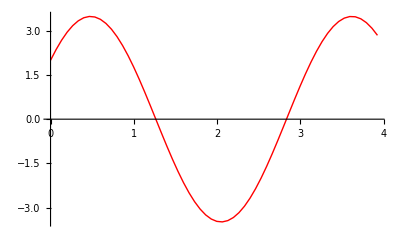

```mathematica
ListPlot[txgrid,PlotRange->All,PlotStyle->{{Red,Thick}},Joined->True]
```